```mathematica
Append
```

```mathematica
Riffle[Table[StringJoin[Riffle[Prepend[Map[ToString[FromDigits[PadRight[#,32],2]]&,1-ImageData[Binarize[g]]],If[ImageDimensions[g][[2]]==19,ToString[ImageDimensions[g][[1]]],Print["fail"g]]],","]],{g,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}],"\n"]//StringJoin
```

17,65011712,267911168,507248640,471597056,940441600,940441600,1879506944,1879506944,1879506944,1879506944,1879506944,1879506944,1879506944,940441600,940441600,1007419392,507248640,267911168,65011712
14,50331648,520093696,1056964608,50331648,50331648,50331648,50331648,50331648,50331648,50331648,50331648,50331648,50331648,50331648,50331648,50331648,50331648,1072693248,1072693248
15,0,1071644672,1073217536,3932160,1835008,1835008,1835008,3932160,7864320,32505856,132120576,260046848,1040187392,1006632960,2013265920,1879048192,1879048192,2147221504,1073479680
16,0,1073217536,1073217536,7340032,31457280,58720256,251658240,534773760,536346624,3932160,1835008,917504,917504,917504,917504,1835008,3932160,2146959360,2145386496
16,7340032,15728640,66060288,128974848,238026752,204472320,472907776,405798912,942669824,808452096,1882193920,1882193920,2147352576,2147352576,3145728,3145728,3145728,3145728,3145728
16,0,2145386496,2145386496,1610612736,1610612736,1610612736,2139095040,2145386496,7340032,1572864,1835008,786432,786432,786432,786432,1572864,3670016,2146435072,2145386496
17,66846720,268304384,503316480,402653184,939524096,837812224,2013003776,2115895296,2014183424,2013724672,2013724672,1879506944,2013724672,939982848,940441600,505151488,267911168,66060288,0
14,0,2146435072,2146435072,3145728,3145728,6291456,6291456,14680064,29360128,25165824,58720256,117440512,251658240,234881024,469762048,469762048,469762048,469762048,469762048
16,65011712,267911168,202899456,403439616,403439616,403439616,403439616,202899456,132120576,536346624,1010565120,2015232000,1879965696,1879965696,1879965696,2015232000,1010565120,536346624,132120576
17,132120576,535822336,1010302976,940310528,1879834624,1879965696,1879441408,1879965696,1879965696,941490176,1010696192,536215552,130416640,917504,786432,1835008,3670016,1072693248,1071644672
7,0,0,0,0,0,0,939524096,939524096,939524096,0,0,0,0,0,939524096,939524096,939524096,0,0

```mathematica
-Graphics-//ImageDimensions
```

{320,200}

```mathematica
Export[NotebookDirectory[]<>"\\Graphics\\lightwood.dat",Flatten[Map[Round[256#].(256^{2,1,0})&,ImageData[-Graphics-],{2}]],"Integer32"]
```

E:\fasm\chess\\Graphics\lightwood.dat

```mathematica
Export[NotebookDirectory[]<>"\\Graphics\\chessboard.dat",Flatten[Map[Round[256#].(256^{2,1,0})&,ImageData[-Graphics-],{2}]],"Integer32"]
```

E:\fasm\chess\\Graphics\chessboard.dat

```mathematica
Export[NotebookDirectory[]<>"\\Graphics\\dksquare.dat",Flatten[Map[Round[256#].(256^{2,1,0})&,ImageData[-Graphics-],{2}]],"Integer32"]
```

E:\fasm\chess\\Graphics\dksquare.dat

```mathematica
Export[NotebookDirectory[]<>"\\Graphics\\ltsquare.dat",Flatten[Map[Round[256#].(256^{2,1,0})&,ImageData[-Graphics-],{2}]],"Integer32"]
```

E:\fasm\chess\\Graphics\ltsquare.dat

```mathematica
Export[NotebookDirectory[]<>"test.bmp",ImageApply[Mean,-Graphics-]]
```

E:\fasm\chess\test.bmp

```mathematica
im=Import[NotebookDirectory[]<>"test.bmp"];
ima=Import[NotebookDirectory[]<>"testalpha.bmp"];
ima=ImageMultiply[Blur[ImageApply[If[Norm[#1-{1,0,0}]<0.1,1,0]&,ima],3],1.5];
```

```mathematica
N[(255 1+255)/256]
```

1.99219

```mathematica
dim=48;
p=Table[
{ImageResize[ImageTake[im,246+280*c[[1]]+{1,280},10+280*c[[2]]+{1,280}],{dim,dim}],ImageResize[ImageTake[ima,246+280*c[[1]]+{1,280},10+280*c[[2]]+{1,280}],{dim,dim}]}
,{c,{{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5}}}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[1,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[1,1]]]]]]//Length
```

4609

```mathematica
Export[NotebookDirectory[]<>"\\Graphics\\wking.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[1,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[1,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\wqueen.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[2,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[2,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\wrook.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[3,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[3,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\wbishop.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[4,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[4,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\wknight.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[5,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[5,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\wpawn.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[6,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[6,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\bking.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[7,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[7,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\bqueen.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[8,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[8,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\brook.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[9,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[9,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\bbishop.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[10,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[10,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\bknight.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[11,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[11,2]]]]]],"Byte"];
Export[NotebookDirectory[]<>"\\Graphics\\bpawn.dat",Riffle[Append[Round[255*Flatten[Map[Mean,ImageData[p[[12,1]]],{2}]]],0],Round[128*Flatten[ImageData[p[[12,2]]]]]],"Byte"];
```

```mathematica
Riffle
```

```mathematica
ImageAdd[
ImageMultiply[ImageApply[1-#&,p[[8,2]]],p[[8,1]]],
ImageMultiply[p[[8,2]],Image[ConstantArray[{0.75,0.75,0.75},{48,48}]]]
]
```

```mathematica
Remove[list]
```

```mathematica
ImageResize[glist[[2]],{48,48}]
```

-Graphics-

```mathematica
ImageResize[Image[Rasterize[Style["K",FontFamily->"Chess Merida",Background->Red,FontSize->48*32]]],48*5]
```

```mathematica
m=ImageApply[Function[{g,a,b},Identity[Clip[
{
If[Abs[g[[1]]-b[[1]]]<1/100,1+0(g[[1]]+b[[1]])/2,(a[[1]]-b[[1]])/(g[[1]]-b[[1]])],
If[Abs[g[[2]]-b[[2]]]<1/100,1+0(g[[2]]+b[[2]])/2,(a[[2]]-b[[2]])/(g[[2]]-b[[2]])],
If[Abs[g[[3]]-b[[3]]]<1/100,1+0(g[[3]]+b[[3]])/2,(a[[3]]-b[[3]])/(g[[3]]-b[[3]])]
}
]]],{glist[[2]],alist[[2]],alist[[1]]}]
```

```mathematica
Solve[{-441/4-(27 a)/200+(17 b)/100==141,441/4-(13 a)/200+(3 b)/100==90},{a,b}]//N
```

{{a→1568.57,b→2723.57}}

```mathematica
f[n_]:=InterpolatingPolynomial[{{0,1000},{10,2400},{20,3000}},n]
```

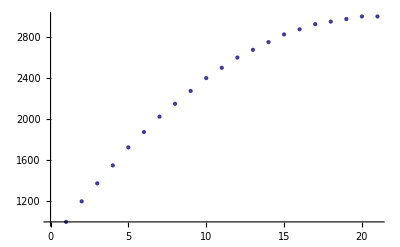

```mathematica
Table[25Round[f[n]/25],{n,0,20}]//ListPlot
```

```mathematica
25Round[f[13]/25]
```

2675

```mathematica
FindDivisions[{850,3150},20]
```

{800,1000,1200,1400,1600,1800,2000,2200,2400,2600,2800,3000,3200}

```mathematica
2 12 256
```

6144

```mathematica
BaseForm[202,16]
```

ca_16

```mathematica
"adsf"
```

```mathematica
im=Image[Map[Round[Mean[#]]&,ImageData[-Graphics-],{2}]];
```

```mathematica
StringJoin[Riffle[Table[
coor[[1]]<>": db "<>StringJoin[Riffle[Map[ToString,Flatten[Map[Round[255 Clip[#,{0,1}]]&,ImageData[ImageResize[ImageTake[im,30+96*coor[[2]]+{1,96},24+96*coor[[3]]+{1,96}],48{1,1}]],{2}]]
],","]]
,{coor,{
{"BlackRookOnWhite",0,0},
{"BlackKnightOnBlack",0,1},
{"BlackBishopOnWhite",0,2},
{"BlackQueenOnBlack",0,3},
{"BlackKingOnWhite",0,4},
{"BlackBishopOnBlack",0,5},
{"BlackKnightOnWhite",0,6},
{"BlackRookOnBlack",0,7},

{"BlackPawnOnWhite",1,1},
{"BlackPawnOnBlack",1,2},
{"WhitePawnOnWhite",4,0},
{"WhitePawnOnBlack",4,1},

{"WhiteRookOnBlack",5,0},
{"WhiteKnightOnWhite",5,1},
{"WhiteBishopOnBlack",5,2},
{"WhiteQueenOnWhite",5,3},
{"WhiteKingOnBlack",5,4},
{"WhiteBishopOnWhite",5,5},
{"WhiteKnightOnBlack",5,6},
{"WhiteRookOnWhite",5,7},

{"EmptyOnWhite",2,0},
{"EmptyOnBlack",2,1},
{"BlackQueenOnWhite",3,3},
{"WhiteQueenOnBlack",2,3},
{"BlackKingOnBlack",3,4},
{"WhiteKingOnWhite",2,4}
}}],"\n"]]
```

```mathematica
7 4 1024
```

28672